# Roseller Periodic Orbits

We want to find periodic orbits of the Rosseler system.  It is going to help us understand the “strange attractor”.

We know we need to use Newtons Method to match points on the Poincare section.

We know how to compute the derivative we need for a Newton step from the sensitivity matrix J.

There is a periodic orbit with winding number 2 near the near-miss orbit (which we found earlier) below.

```mathematica
TMax=14;
CutPlane={Opacity[0.3],Polygon[{{-12,0,0},{12,0,0},{12,0,20},{-12,0,20}}]};
yStart={-4.743977711024888,0,0.019234252282450195};
yStartSol=NDSolveValue[{
y'[t]==f[{0.2,0.2,5.7}][y[t]], y[0]==yStart},y,{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦2⟧==0,"Direction"->-1}];
yMid=Chop[yStartSol["ValuesOnGrid"]⟦-1⟧]; tMid=yStartSol["Coordinates"]⟦1,-1⟧;
yEndSol=NDSolveValue[{
y'[t]==f[{0.2,0.2,5.7}][y[t]], y[0]==yMid},y,{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦2⟧==0,"Direction"->-1}];
yEnd=Chop[yEndSol["ValuesOnGrid"]⟦-1⟧]; tEnd=yEndSol["Coordinates"]⟦1,-1⟧;
Show[
ParametricPlot3D[yStartSol[t],{t,0, tMid},PlotStyle->Red],
ParametricPlot3D[yEndSol[t],{t,0, tEnd},PlotStyle->Blue],
Graphics3D[{CutPlane,PointSize[0.015] ,{Red,Point[yStart]},{Blue,Point[yMid]},{Cyan,Point[yEnd]}}],
PlotRange->All
]
```

-Graphics3D-

Here is an ode Solver that goes round “wMax” times before it stops.

```mathematica
w=0;
yStartSol=Reap[NDSolveValue[{
y'[t]==f[{0.2,0.2,5.7}][y[t]], y[0]==yStart,
J'[t]==df[{0.2,0.2,5.7}][y[t]].J[t], J[0]==IdentityMatrix[3]},{},{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦2⟧==0,"Direction"->-1,
"EventAction":>(Sow[{y[t],J[t]}];"StopIntegration")}]]
```

NDSolveValue::noout: No functions were specified for output from NDSolveValue.

{{},{{{{-8.31059,-6.10623×10^-15,0.0143196},{{1.30255,-0.00223928,-0.124124},{0.284465,1.75067,-0.0112322},{0.00135792,0.000126559,-0.000128232}}}}}}

```mathematica
(* Making Pics *)
CurvePic=ParametricPlot3D[ ySol[t],{t,0, TMax},PlotRange->All,BoxRatios->{1,1,1}];
CutPlane={Opacity[0.3],Polygon[{{-12,0,0},{12,0,0},{12,0,20},{-12,0,20}}]};
Show[CurvePic,
Graphics3D[{
{Opacity[0.3],CutPlane},
{Red,PointSize[0.03],Point[DotData]}
}]]
```

-Graphics3D-

```mathematica
Chop[DotData]
```

{{-4.74398,0,0.0192343},{-8.31059,0,0.0143196},{-4.35985,0,0.019981}}

## Definitions

The VDP system has one periodic orbit and the Rosseler system looks like it might have periodic orbits.  First we need to define a periodic orbit and a thing called a winding number.

Orbit of ODE (Informal Definition)
The solution of an ODE y'=f(y) defined by a choice of y(0)=y_0 is called an orbit.

Periodic Orbit of ODE (Informal Definition)
An orbit of the ODE y'=f(y) is periodic if for some T>0 we have  y(t)=y(t+T) for all t.The period is the smallest possible T.

Map (Informal Definition)
A map is function g:ℝ^n→ℝ^n. An orbit is the sequence y_(k+1)=g(y_k) defined by a choice of y_0∈ℝ^n.

Periodic Orbit of Map (Informal Definition)
The orbit y_(k+1)=g(y_k) is periodic if for some K≥1 we have y_k=y_(k+K) for all k.  The period is the smallest possible K.

## Periodic Orbits for VDP

The VDP system is
	y1' | = | y2                               
y2' | = | μ(1-y1^2)y2-y1
clearly has a periodic orbit which sucks all the solutions in.  We can approximate a point on this periodic orbit by running the ODE solver and grabbing any value well out in the orbit.

```mathematica
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
Df[μ_][{x_,v_}]:={{0,1},{-1-2v x μ,μ (1-x^2)}}
TMax=64.5;y0={0,0.1};μ=0.2; ϵ=1;
ySol=NDSolveValue[{
y'[t]==f[μ][y[t]],y[0]==y0
},y,{t,0, TMax}
];
TabView[{
"Phase Space"->ParametricPlot[ySol[t],{t, 0, TMax},
PlotLabel->ySol[TMax]],
"y_1& y_2"->Plot[ySol[t],{t, 0, TMax},
PlotLabel->ySol[TMax]]
},2]
```

12

We can estimate the period from a graph.

```mathematica
ySol[TMax]
```

{1.99887,-0.0466208}

```mathematica
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
Df[μ_][{x_,v_}]:={{0,1},{-1-2v x μ,μ (1-x^2)}}
TMax=6.28;y0={0,0.1};μ=0.2; ϵ=1;
yPer={1.9988653139089454,-0.04662080536264521}
ySol=NDSolveValue[{
y'[t]==f[μ][y[t]],y[0]==yPer
},y,{t,0, TMax}
];
TabView[{
"Phase Space"->ParametricPlot[ySol[t],{t, 0, TMax},
PlotLabel->ySol[TMax]],
"y_1& y_2"->Plot[ySol[t],{t, 0, TMax},
PlotLabel->ySol[TMax],
GridLines->{Automatic,yPer}]
},2]
```

{1.99887,-0.0466208}

12

We can compute it accurately using a variety of numerical tricks.

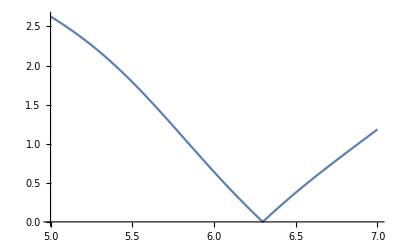

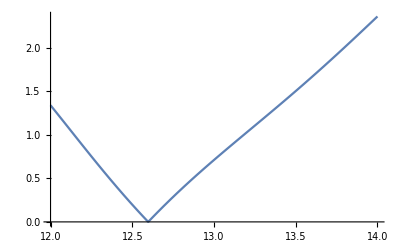

```mathematica
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
Df[μ_][{x_,v_}]:={{0,1},{-1-2v x μ,μ (1-x^2)}}
TMax=15.2;y0={0,0.1};μ=0.2; ϵ=1;
yPer={1.9988653139089454,-0.04662080536264521};
ySol=NDSolveValue[{
y'[t]==f[μ][y[t]],y[0]==yPer
},y,{t,0, TMax}
];
Plot[Norm[ySol[t]-yPer],{t,5,7}]
Plot[Norm[ySol[t]-yPer],{t,12,14}]
```

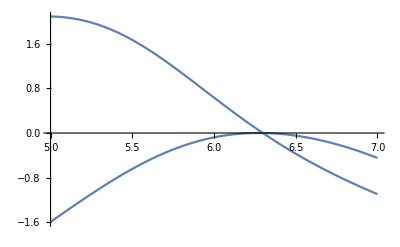

```mathematica
Plot[ySol[t]-yPer,{t,5,7}]
```

```mathematica
tSub=FindRoot[ySol[t][[2]]==yPer[[2]], {t, 6.2}]
ySol[t]/.tSub
yPer
```

Part::partw: Part 2 of InterpolatingFunction[{{0.,7.2}},{5,3,1,{125},{4},0,0,0,0,Automatic,«3»},{{0.,«9»,«115»}},{{{1.99887,-0.0466208},{-0.0466208,-1.97094}},«9»,«115»},{Automatic}][t] does not exist.

{t→6.29869}

{1.99958,-0.0466208}

{1.99887,-0.0466208}

Another way to do this is using the EventLocator

```mathematica
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
Df[μ_][{x_,v_}]:={{0,1},{-1-2v x μ,μ (1-x^2)}}
TMax=7.2;y0={0,0.1};μ=0.2; ϵ=1;
yPer={1.9988653139089454,-0.04662080536264521};
ySol=NDSolveValue[{
y'[t]==f[μ][y[t]],y[0]==yPer
},y,{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦2⟧==yPer⟦2⟧,Direction->-1,"EventAction":> Print[t]}]
```

Part::partw: Part 2 of y[t] does not exist.

6.29869

InterpolatingFunction[…]

Are there any other periodic orbits?  We are going to talk about this in class.

## Periodic orbits for the Rosseller System

As we saw before, there seem to be a lot of near misses for periodic orbits.  Are there periodic orbits?  There are a lot of things we don’t  know when searching for a periodic orbit: where it starts and stops y_0 and the period T.

One way to find periodic a periodic orbit is to start with a near miss. We can probably find a near miss if we mess around down near the flat bit of the “attractor”.

I really did get what is below just messing around!  There is something very close to a periodic orbit here because it looks like the curves merge.  In a top view you can see that it is close but not perfect.

```mathematica
Clear[ f,df,y1,y2,y3,a,b,c]
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
df[{a_,b_,c_}][{y1_,y2_,y3_}]:={{0,-1,-1},{1,a,0},{y3,0,-c+y1}}
StdParams={0.2,0.2,5.7};  TMax=25.0;
y0={4.98,5.01,1};
ySol=NDSolveValue[{
y'[t]==f[{0.2,0.2,5.7}][y[t]], y[0]==y0},y,{t,0, TMax}];


CurvePic=ParametricPlot3D[ ySol[t],{t,0, TMax},PlotRange->All,BoxRatios->{1,1,1}];
Manipulate[
Show[CurvePic,
Graphics3D[{PointSize[0.03],{Red, Point[ySol[t1]]},{Cyan, Point[ySol[t2]]}}],
PlotLabel->{ySol[t1],ySol[t2]}],
{{t1,0}, 0, TMax},
{{t2,TMax/2}, 0, TMax}
]
```

We can isolate the near miss part and make a function that will let is tweak the starting point. We can then fix the “almost” part by tweaking the values carefully. Right now there are four things (the three starting coordinates {y_1,y_2,y_3} and the time “t” to tweak.  The  cross-section idea will reduce this to two!

```mathematica
TMax=14;
ySolPar=ParametricNDSolveValue[{
y'[t]==f[{0.2,0.2,5.7}][y[t]], y[0]=={y1,y2,y3}},y,{t,0, TMax},{y1,y2,y3}];
ParametricPlot3D[ySolPar[-2.95,3.45,0.025][t],{t,0, TMax},PlotRange->All]
```

-Graphics3D-

There is clearly a two-loop periodic orbit somewhere nearby. To tie it down we need to find a way to compute the period T  and the starting/stopping point that makes it match perfectly.  We are not going to stumble over accurate values of these four unknowns! We need equations and if possible we should reduce the number of unknowns. Something like this is why the sections idea was created.

```mathematica
TMax=14;
ySol=NDSolveValue[{
y'[t]==f[{0.2,0.2,5.7}][y[t]], y[0]=={-2.95,3.45,0.025}},y,{t,0, TMax}];

(* Making pics *)
CurvePic=ParametricPlot3D[ ySol[t],{t,0, TMax},PlotRange->All,BoxRatios->{1,1,1}];
CutPlane={Opacity[0.3],Polygon[{{-12,0,0},{12,0,0},{12,0,20},{-12,0,20}}]};
Manipulate[
Show[CurvePic,Graphics3D[CutPlane],
Graphics3D[{PointSize[0.03],{Red, Point[ySol[t1]]},{Cyan, Point[ySol[t2]]}}],
PlotLabel->{ySol[t1],ySol[t2]}],
{{t1,0}, 0, TMax},
{{t2,TMax}, 0, TMax}
]
```

We could try to make the paired cut points on the plane coincide!  If we do that we find the period orbit and with only two parameters -- the coordinates in the plane.  We could use other planes but y_2==0 should work.

I am going to use the event locator to get the paired points in the plane.

```mathematica
TMax=14;
{ySol,{DotData}}=Reap[NDSolveValue[{
y'[t]==f[{0.2,0.2,5.7}][y[t]], y[0]=={-2.95,3.45,0.025}},y,{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦2⟧==0,"Direction"->-1,"EventAction":>Sow[y[t]]}]];

(* Making Pics *)
CurvePic=ParametricPlot3D[ ySol[t],{t,0, TMax},PlotRange->All,BoxRatios->{1,1,1}];
CutPlane={Opacity[0.3],Polygon[{{-12,0,0},{12,0,0},{12,0,20},{-12,0,20}}]};
Show[CurvePic,
Graphics3D[{
{Opacity[0.3],CutPlane},
{Red,PointSize[0.03],Point[DotData]}
}]]
```

-Graphics3D-

We want to take either the first or third point as our guess.  I am going to compute the curve and the sensitivity matrix J this time.

```mathematica
df[{a_,b_,c_}][{y1_,y2_,y3_}]:={{0,-1,-1},{1,a,0},{y3,0,-c+y1}}
y0=Chop[DotData⟦1⟧];
{ySol,{yJData}}=Reap[NDSolveValue[{
y'[t]==f[{0.2,0.2,5.7}][y[t]], y[0]==y0,
J'[t]==df[{0.2,0.2,5.7}][y[t]].J[t], J[0]==IdentityMatrix[3]},y,{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦2⟧==0,"Direction"->-1,"EventAction":>Sow[{y[t],J[t]}]}]];
{PPoint,PJ}=yJData⟦2⟧

(* Making Pics *)
ϵ=0.4;
CurvePic=ParametricPlot3D[ ySol[t],{t,0, TMax},PlotRange->All,BoxRatios->{1,1,1}];
CutPlane={Opacity[0.3],Polygon[{{-12,0,0},{12,0,0},{12,0,20},{-12,0,20}}]};
Show[CurvePic,
Graphics3D[{
{Opacity[0.3],CutPlane},
{Red,Ellipsoid[y0,ϵ IdentityMatrix[3]]},
{Green,PointSize[0.05],Point[PPoint]}
}]]
SingularValueList[PJ]
```

{{-4.35985,2.08167×10^-16,0.019981},{{-3.28183,0.0174557,0.312844},{3.38404,0.905368,-0.314217},{-0.00585568,0.000235574,0.000560054}}}

-Graphics3D-

{4.77838,0.637075}

One of the singular values is so small that the software has decided it is zero! This means the sphere has been mapped around and squashed until it is essentially flat!  We only care about input in the vertical plane and we only care about outputs in the vertical plane.  Restricted to the plane our 2×2 sensitivity/derivative matrix  and its singular values are.

```mathematica
P2J=Transpose[({{1, 0}, {0, 0}, {0, 1}})].PJ.({{1, 0}, {0, 0}, {0, 1}})
SingularValueList[P2J]
```

{{-3.99068,0.394725},{-0.00558739,0.000554417}}

{4.01016,1.74968×10^-6}

The question is how can we use this derivative information to compute a periodic orbit.

```mathematica
y0=Chop[DotData⟦1⟧]
TMax=14;
ySol=ParametricNDSolveValue[
{y'[t]==f[{0.2,0.2,5.7}][y[t]], y[0]=={y1,0,y3}},
{y},
{t,0, TMax},
{y1,y3},
Method->{"EventLocator", "Event":>y[t]⟦2⟧==0,"Direction"->-1,
"EventAction":>Sow[{t,y[t]}]}]
ForwardMap[{y_,z_}]:= Reap[ySol[y,z];]⟦2,1,-1,2,{1,3}⟧
ForwardMap[{-4.359853462863213,0.019980952714422642}]
FindRoot[ForwardMap[{y,z}]=={y,z},{{y,-4.36},{z,0.02}}]
```

{-4.35985,0,0.019981}

ParametricFunction[<>]

{-5.78268,0.0174881}

Part::partw: Part 1 of {} does not exist.

FindRoot::nlnum: The function value {4.36+{Null,{}}⟦2,1,-1,2,{1,3}⟧,-0.02+{Null,{}}⟦2,1,-1,2,{1,3}⟧} is not a list of numbers with dimensions {2} at {y,z} = {-4.36,0.02}.

FindRoot[ForwardMap[{y,z}]=={y,z},{{y,-4.36},{z,0.02}}]

```mathematica
NDSolveValue[{
y'[t]==f[{0.2,0.2,5.7}][y[t]], y[0]==y0,
J'[t]==df[{0.2,0.2,5.7}][y[t]].J[t], J[0]==IdentityMatrix[3]},y,{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦2⟧==0,"Direction"->-1,"EventAction":>Sow[{y[t],J[t]}]}]];
```